# Inlämningsuppgift 1: Problemlösning

## Lösningar

### Polynomekvation

För att hitta lösningarna till polynomekvationen: 2 x^4+28/3 x^3-22/3 x^2-140/3 x+16=0. 
Använder jag funktionen Solve[] där den ska lösa variabeln x.

```mathematica
{x1,x2,x3,x4}=x/.Solve[2 x^4+28/3 x^3-22/3 x^2-140/3 x+16==0]
```

{-4,-3,1/3,2}

Jag använder x1, x2 ... för att spara ekvationens nollställen/skärningspunkter på de värderna för att sedan använda dem när jag ska rita grafen.

För att plotta grafen används funktionen Plot, där jag använder Axeslabel för att ge horisontal planet namnet x och vertikal planet till y. Epilog används för att få punkter på nollställena där efter väljer jag färgen röd samt punkternas storlek och vart punkterna ska vara någonstans (Point)

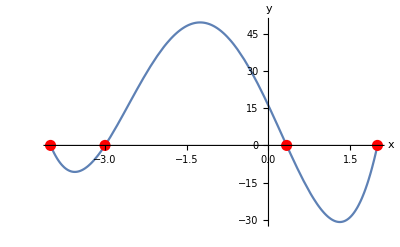

```mathematica
Plot[2 x^4+(28 x^3)/3-(22 x^2)/3-(140 x)/3+16,{x,2,-4},AxesLabel->{"x","y"},Epilog ->{Red,PointSize[0.02],
Point[{x1,0}],
Point[{x2,0}],
Point[{x3,0}],
Point[{x4,0}]
}
]
```

### Olikhet

### Binomisk ekvation

```mathematica
För att hitta lössningarna till den komplexa ekvationen: z=-3+3i
```

```mathematica
AbsArg[(-3+3I)^5]
```

{972 √2,-π/4}

```mathematica
r^5 *(cos5v + Isin5v)==z^5
```

```mathematica
z1=z^5==-3+3I
```

z^5==-3+3 ⅈ

```mathematica
Abs[z1]
```

Abs[z^5==-3+3 ⅈ]

```mathematica
{z1,z2,z3,z4,z5}=z/.Solve[z^5 == -3 + 3*I]
```

{(-3+3 ⅈ)^(1/5),(-3+3 ⅈ)^(1/5) (-1)^(2/5),-(-3+3 ⅈ)^(1/5) (-1)^(3/5),(-3+3 ⅈ)^(1/5) (-1)^(4/5),-(-3)^(1/5) (-1+ⅈ)^(1/5)}

```mathematica
Re[z1]
```

Re[(-3+3 ⅈ)^(1/5)]

```mathematica
Re[z2]
```

Re[(-3+3 ⅈ)^(1/5) (-1)^(2/5)]

```mathematica
Re[z3]
```

Re[-(-3+3 ⅈ)^(1/5) (-1)^(3/5)]

```mathematica
Re[z4]
```

Re[(-3+3 ⅈ)^(1/5) (-1)^(4/5)]

```mathematica
Re[z5]
```

Re[-(-3)^(1/5) (-1+ⅈ)^(1/5)]

```mathematica
Im[z1]
```

### Arean av en cirkel och närmevärde till Pi

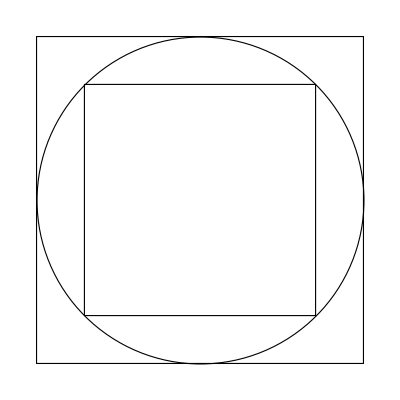

```mathematica
Show[Graphics[{FaceForm[None],EdgeForm[{Black}],Polygon[{{-1/Sqrt[2],-1/Sqrt[2]},{-1/Sqrt[2],1/Sqrt[2]},{1/Sqrt[2],1/Sqrt[2]} ,{1/Sqrt[2], -1/Sqrt[2]}}],Disk[{0, 0}],Polygon[{{-1, -1}, {-1, 1},{1, 1},{1, -1}}]}]]
```